# Auditory Game of Life/ Game of Life & Music

## CSC/MTH 205 Spring 2018 Final Project Neamat Sabry

## Project Description

### Background

This project is an extension of the game of life app we created in class. It is intended to be interactive, where the user clicks on grid cells to make it black or white, as well as auditory, where one hopefully inputs a specific pattern of the game of life and the app changes it to audio (with different pitches and pairings according to whether a cell is alive or dead). I’m interested to see if there are any patterns within the sound created for every game of life pattern (and if there are any repetitions) and if the sound harmonizes enough to make a nice melody.

### Next Steps

The next steps for this project is to first integrate the mouse interaction to the Game of Life’s grid and, once that is working well, I need to work more with Mathematica Audio and figure out how to apply it to the app.

### Project Skeleton

Mostly Homework 6, but with the added applications in mind.  You’ll find it below the Code Section.

### Some experiments with sound and audio

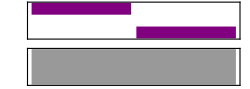

```mathematica
Sound[{SoundNote["A"],SoundNote["G"]}]
```

```mathematica
Sound[{Play[Sin[1000 t (1+t^2)],{t,0,.2}],Play[Sin[500 t (1+t^3)],{t,0,.5}]}]
```

-Graphics-

```mathematica
s=Sound[Table[SoundNote[i],{i,0,12}],{0,1.5}];
```

```mathematica
s2=Sound[Table[SoundNote[12-i],{i,0,12}],{0.5,2}];
```

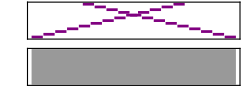

```mathematica
Sound[{s,s2}]
```

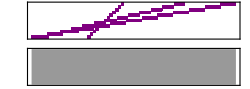

```mathematica
Sound[{Sound[s,{0,2}],Sound[s,{.5,1.5}],Sound[s,{.7,.9}]}]
```

And it has all sorts of instruments too!

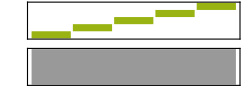

```mathematica
Sound[{"Accordion",Table[SoundNote[i],{i,5}]}]
```

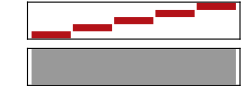

```mathematica
Sound[{"Flute",Table[SoundNote[i],{i,5}]}]
```

And have multiple instruments play together

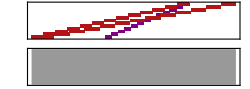

```mathematica
Sound[{"Flute",Sound[s,{0,1}],"Trumpet",Sound[s,{.2,1.3}],"Piano",Sound[s,{.7,1}]}]
```

### Project “skeleton” following:

## Code

### Calculate number of neighbors around current cell

```mathematica
nrOfNeighbors[a_,i_,j_]:=Module[{nrRows,nrCols,nr,neighbors={0}},
{nrRows,nrCols}=Dimensions[a];
Which[
(* center*)
i≥2 &&i<nrRows&&j≥2&&j<nrCols,
neighbors={
a[[i-1,j-1]],a[[i-1,j]],a[[i-1,j+1]],
a[[i,j-1]],a[[i,j+1]],
a[[i+1,j-1]],a[[i+1,j]],a[[i+1,j+1]]
},
(*corner top left *)
i==1&&j==1,
neighbors={a[[1,2]],a[[2,1]],a[[2,2]]},
(*corner top right *)
i==1&&j== nrCols,
neighbors={a[[1,j-1]],a[[2,j-1]],a[[2,j]]},
(*corner bottom left *)
i== nrRows&&j== 1,
neighbors={a[[i,2]],a[[i-1,1]],a[[i-1,2]]},
(*corner bottom right *)
i==nrRows&&j== nrCols,
neighbors={a[[i,j-1]], a[[i-1, j]],a[[i-1,j-1]]},
(*border top  *)
i==1 && j≥ 2 && j<nrCols,
neighbors={a[[1,j-1]],a[[1,j+1]],a[[2,j]],a[[2,j-1]],a[[2,j+1]]},
(*border bottom*)
i==nrRows && j≥ 2 && j<nrCols,
neighbors={a[[i,j-1]],a[[i,j+1]],a[[i-1,j]],a[[i-1,j-1]],a[[i-1,j+1]]},
(*border left*)
j==1 && i≥ 2 && i<nrRows,
neighbors={a[[i-1,1]],a[[i+1,1]],a[[i,2]],a[[i-1,2]],a[[i+1,2]]},
(*border right*)
j==nrCols && i≥ 2 && i <nrRows,
neighbors={a[[i-1,j]],a[[i+1,j]],a[[i,j-1]],a[[i-1,j-1]],a[[i+1,j-1]]}
];
nr=Total[neighbors]
];
```

```mathematica
nrOfNeighborsRule2[a_,i_,j_]:=Module[{nrRows,nrCols,nr,neighbors={0}},
{nrRows,nrCols}=Dimensions[a];
Which[
(* center*)
i≥2 &&i<nrRows&&j≥2&&j<nrCols,
neighbors={
a[[i-1,j]],a[[i,j-1]],
a[[i,j+1]],a[[i+1,j]]
},
(*corner top left *)
i==1&&j==1,
neighbors={a[[1,2]],a[[2,1]]},
(*corner top right *)
i==1&&j== nrCols,
neighbors={a[[1,j-1]],a[[2,j]]},
(*corner bottom left *)
i== nrRows&&j== 1,
neighbors={a[[i,2]],a[[i-1,1]],a[[i-1,2]]},
(*corner bottom right *)
i==nrRows&&j== nrCols,
neighbors={a[[i,j-1]], a[[i-1, j]],a[[i-1,j-1]]},
(*border top  *)
i==1 && j≥ 2 && j<nrCols,
neighbors={a[[1,j-1]],a[[1,j+1]],a[[2,j]],a[[2,j-1]],a[[2,j+1]]},
(*border bottom*)
i==nrRows && j≥ 2 && j<nrCols,
neighbors={a[[i,j-1]],a[[i,j+1]],a[[i-1,j]],a[[i-1,j-1]],a[[i-1,j+1]]},
(*border left*)
j==1 && i≥ 2 && i<nrRows,
neighbors={a[[i-1,1]],a[[i+1,1]],a[[i,2]],a[[i-1,2]],a[[i+1,2]]},
(*border right*)
j==nrCols && i≥ 2 && i <nrRows,
neighbors={a[[i-1,j]],a[[i+1,j]],a[[i,j-1]],a[[i-1,j-1]],a[[i+1,j-1]]}
];
nr=Total[neighbors]
];
```

### Status (whether dead or alive in next generation) for current cell

```mathematica
nextIJposiiton[a_,i_,j_]:=Module[{crtCell,cellStatus},
cellStatus=0;
crtCell = a[[i,j]];
Which[
(*if crtCell is alive and has 2 or 3 neighbors, then it will live*)
(crtCell== 1 && (nrOfNeighbors[a,i,j]==  3 || nrOfNeighbors[a,i,j]== 2)) , 
cellStatus=1,
(*if crtCell is alive and has more than 3 neighbors, it will die*)
crtCell== 1 && nrOfNeighbors[a,i,j] > 3 , 
cellStatus=0,
(*if crtCell is alive and has fewer than 2 neighbors, it will die*)
crtCell== 1 && nrOfNeighbors[a,i,j] < 2 , 
cellStatus=0,
(*if crtCell is dead and has exactly 3 neighbors, it will be reborn*)
crtCell== 0 && nrOfNeighbors[a,i,j]==  3, 
cellStatus=1
];
cellStatus
];
```

### Compute next generation of cells

```mathematica
nextGen[a_]:=Module[{newList,nrRows,nrCols,i,j,newA},
(*get dimensions of the grid*)
{nrRows,nrCols}=Dimensions[a];
(*redefine list a as newA*)
newList = a;
(*loop through cells in grid*)
For[i=1,i≤ nrRows,i++,
For[j=1,j≤ nrCols,j++,
newList[[i,j]]=nextIJposiiton[a,i,j];
];
];
newList
]
```

## Graphics

```mathematica
drawGameOfLife[n1_,n2_,myArray_]:=Module[{colors,i,j,myDrawing},
colors=ConstantArray[0,{n1,n2}];
For[i=1,i≤ n1,i++,For[j=1,j≤ n2,j++,If[myArray[[i,j]]== 0,colors[[i,j]]=White,colors[[i,j]]=Black];
]];
myDrawing={EdgeForm[Directive[Thick,Cyan]],Table[{colors[[i,j]],Rectangle[{i,j}]},{i,1,n1},{j,1,n2}]};
Graphics[myDrawing]
]
```

## App

```mathematica
gameOfLifeApp[n1_,n2_]:=
DynamicModule[{newList, initList},
initList=RandomInteger[1,{n1,n2}];
newList=initList;
Manipulate[
drawGameOfLife[n1,n2,newList],
Button["NEXT",
newList=nextGen[newList];
drawGameOfLife[n1,n2,newList]
],
Button["RESET",
newList=initList
],
Button["NEW",
initList=RandomInteger[1,{n1,n2}];
newList=initList;
],
Button["PRINT",
Print[MatrixForm[newList]]
]
]
]
```

## Initiate Variables

```mathematica
GRIDSIZE=20;
```

## Run

```mathematica
gameOfLifeApp[GRIDSIZE,GRIDSIZE]
```